## Frenkel defect MD trajectory analysis

#### Import data

```mathematica
SetDirectory ["/Volumes/MicroSD/Dropbox/PostDoc_SD/mathematica/ZrC_analysis/MD-trajectory"];
fileMD={"def_traj_cart_periodic-Frenkel_500_222kp-6hr-9.700"};
dataMD= Table[ReadList[fileMD[[i]],Table[Number,{i,1,96}]],{i,1,Length[fileMD]}][[1]];
```

```mathematica
dataMD[[1]]//Dimensions
```

{96}

```mathematica
hurst=Table[FindProcessParameters[dataMD[[i]],FractionalBrownianMotionProcess[h]],{i,1,96}];
```

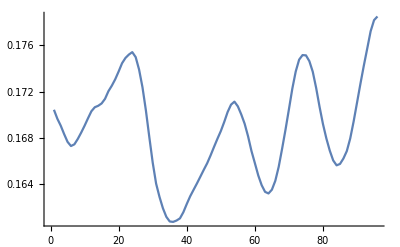

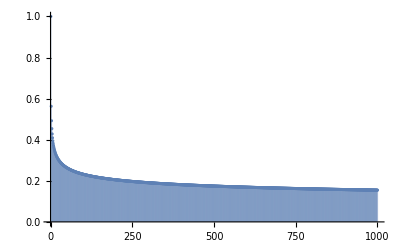

```mathematica
ListLinePlot[h/.hurst]
ListPlot[Table[CorrelationFunction[FractionalBrownianMotionProcess[h]/.hurst[[1]],1,j],{j,1000}],Filling->Axis,PlotRange->All]
```

#### Partition data

For each element in the time-series, partition in three elements, x, y and z.

```mathematica
dataXYZ=Transpose[Table[Partition[dataMD[[i]],3],{i,1,1024}]];
dataXYZ10=Transpose[Table[Partition[dataMD[[i]],3],{i,1,10}]];
dataXYZ250=Transpose[Table[Partition[dataMD[[i]],3],{i,1,250}]];
dataXYZ300=Transpose[Table[Partition[dataMD[[i]],3],{i,1,300}]];
dataXYZ500=Transpose[Table[Partition[dataMD[[i]],3],{i,1,500}]];
dataXYZ750=Transpose[Table[Partition[dataMD[[i]],3],{i,1,750}]];
dataXYZ1000=Transpose[Table[Partition[dataMD[[i]],3],{i,1,1000}]];
```

#### Plot

```mathematica
plotOpts={BoxRatios->{1,1,1},PlotStyle->PointSize[0.01],ImageSize->Large};
```

```mathematica
ListPointPlot3D[dataXYZ,PlotRange->{Automatic,Automatic,{-1,9}},plotOpts]
```

-Graphics3D-

```mathematica
Transpose@Drop[Transpose@Partition[dataMD[[1]],3],1]
```

{{2.2001,4.5973},{1.2695,3.57},{7.2025,7.2617},{7.1944,7.2697},{2.3953,7.2186},{2.3888,7.2433},{7.2455,2.4442},{7.2208,2.4507},{2.4413,2.3983},{7.1966,4.8507},{7.1383,4.8644},{2.3895,4.8209},{7.2263,0.037},{7.2515,0.0565},{2.413,0.0275},{2.4293,-0.1351},{4.8025,7.2379},{4.783,7.2126},{-0.0865,7.2675},{-0.1002,7.3258},{4.812,2.4265},{4.8992,2.4102},{0.0186,2.45},{4.7885,4.8265},{4.7598,4.8078},{-0.104,4.8681},{-0.1681,4.9323},{4.8322,0.0074},{4.8121,0.0275},{0.013,0.051},{0.0317,0.0797},{7.1837,4.8593}}

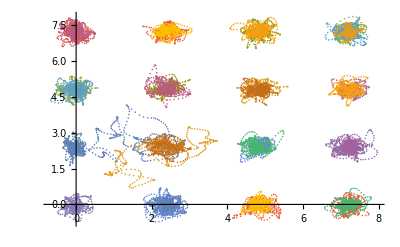

```mathematica
dataXYZ2d=Transpose[Table[Transpose@Drop[Transpose@Partition[dataMD[[i]],3],-1],{i,1,500}]];
ListPlot@%
```

```mathematica
Show[{ListPointPlot3D[dataXYZ500[[1;;2]],PlotRange->{Automatic,Automatic,Automatic},plotOpts],ListPointPlot3D[dataXYZ500[[7]]]}]
```

-Graphics3D-

```mathematica
ListPointPlot3D[dataXYZ250,PlotRange->{Automatic,Automatic,{-1,9}},plotOpts]
```

-Graphics3D-

```mathematica
ListPointPlot3D[dataXYZ500,PlotRange->{Automatic,Automatic,{-1,9}},plotOpts]
```

-Graphics3D-

```mathematica
ListPointPlot3D[dataXYZ750,PlotRange->{Automatic,Automatic,{-1,9}},plotOpts]
```

-Graphics3D-

```mathematica
ListPointPlot3D[dataXYZ1000,PlotRange->{Automatic,Automatic,{-1,9}},plotOpts]
```

-Graphics3D-

#### Selected atoms

```mathematica
(*4=NN=Red,Green=3,2=Interstitial,1=NN*)
(*Interstitial, NN1(mobile), NN2(static),NNN*)
```

```mathematica
ListPointPlot3D[dataSelected,PlotRange->{{-1,9},{-1,9},{-1,9}},plotOpts]
```

ListPointPlot3D::arrayerr: dataSelected must be a valid array or a list of valid arrays.

General::stop: Further output of ListPointPlot3D::arrayerr will be suppressed during this calculation.

ListPointPlot3D[dataSelected,PlotRange→{{-1,9},{-1,9},{-1,9}},{BoxRatios→{1,1,1},PlotStyle→PointSize[0.01],ImageSize→Large}]

```mathematica
plotOpts={BoxRatios->{1,1,1},PlotStyle->PointSize[0.01],ImageSize->Large};
plotOpts2={BoxRatios->{1,1,1},PlotStyle->{Green,PointSize[0.01]},ImageSize->Large};
plotOpts3={BoxRatios->{1,1,1},PlotStyle->{Red,PointSize[0.01]},ImageSize->Large};
```

```mathematica
(*4=NN=Red,Green=3,2=Interstitial,1=NN*)
(*Interstitial, NN1(mobile), NN2(static),NNN*)
dataSelected={dataXYZ[[2]],dataXYZ[[1]],dataXYZ[[27]],dataXYZ[[25]]};
```

```mathematica
dataSelected10={dataXYZ[[2]][[1;;10]],dataXYZ[[1]][[1;;10]],dataXYZ[[27]][[1;;10]],dataXYZ[[25]][[1;;10]]};
dataSelected250={dataXYZ[[2]][[10;;250]],dataXYZ[[1]][[10;;250]],dataXYZ[[27]][[10;;250]],dataXYZ[[25]][[10;;250]]};
dataSelected500={dataXYZ[[2]][[1;;500]],dataXYZ[[1]][[1;;500]],dataXYZ[[27]][[1;;500]],dataXYZ[[25]][[1;;500]]};
dataSelected750={dataXYZ[[2]][[1;;750]],dataXYZ[[1]][[1;;750]],dataXYZ[[27]][[1;;750]],dataXYZ[[25]][[1;;750]]};
dataSelected1000={dataXYZ[[2]][[1;;1000]],dataXYZ[[1]][[1;;1000]],dataXYZ[[27]][[1;;1000]],dataXYZ[[25]][[1;;1000]]};
```

```mathematica
p1=ListPointPlot3D[dataSelected10,PlotRange->{{-1,9},{-1,9},{-1,9}},plotOpts]
p2=ListPointPlot3D[dataSelected250,PlotRange->{{-1,9},{-1,9},{-1,9}},plotOpts]
p3=ListPointPlot3D[dataSelected500,PlotRange->{{-1,9},{-1,9},{-1,9}},plotOpts]
p4=ListPointPlot3D[dataSelected750,PlotRange->{{-1,9},{-1,9},{-1,9}},plotOpts]
p5=ListPointPlot3D[dataSelected1000,PlotRange->{{-1,9},{-1,9},{-1,9}},plotOpts]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«2 more identical outputs»

```mathematica
ListPointPlot3D[dataSelected500[[1]],PlotRange->{{-1,9},{-1,9},{-1,9}},plotOpts,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
dataSelected10YZ=Table[Transpose[{Transpose[dataSelected10[[i]]][[2]],Transpose[dataSelected10[[i]]][[3]]}],{i,1,4}];
dataSelected250YZ=Table[Transpose[{Transpose[dataSelected250[[i]]][[2]],Transpose[dataSelected250[[i]]][[3]]}],{i,1,4}];
dataSelected500YZ=Table[Transpose[{Transpose[dataSelected500[[i]]][[2]],Transpose[dataSelected500[[i]]][[3]]}],{i,1,4}];
dataSelected750YZ=Table[Transpose[{Transpose[dataSelected750[[i]]][[2]],Transpose[dataSelected750[[i]]][[3]]}],{i,1,4}];
dataSelected1000YZ=Table[Transpose[{Transpose[dataSelected1000[[i]]][[2]],Transpose[dataSelected1000[[i]]][[3]]}],{i,1,4}];
selectedData={dataSelected10YZ,dataSelected250YZ,dataSelected500YZ,dataSelected750YZ,dataSelected1000YZ};
```

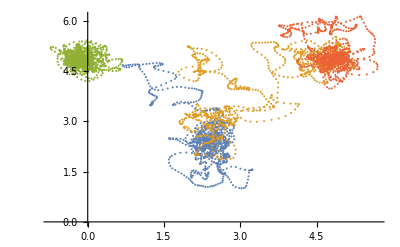

```mathematica
ListPlot[dataSelected1000YZ[[1;;4]]]
```

```mathematica
plotOpts3={PlotRange->{{-0.9,6},{0.9,6.4}},FrameLabel->{"y ()","z"},Frame->True,AspectRatio->1,PlotLegends->Placed[{"Ci","Cnn1","Cnn2","Cnnn"},{0.85,0.25}]};
q1=ListLinePlot[dataSelected10YZ,plotOpts3];
q2=ListLinePlot[dataSelected250YZ,plotOpts3];
q3=ListLinePlot[dataSelected500YZ,plotOpts3];
q4=ListLinePlot[dataSelected750YZ,plotOpts3];
q5=ListLinePlot[dataSelected1000YZ,plotOpts3];
```

```mathematica
grid2d=GraphicsGrid[{{q2,q3,q4,q5}},ImageSize->1200,Spacings->-5];
```

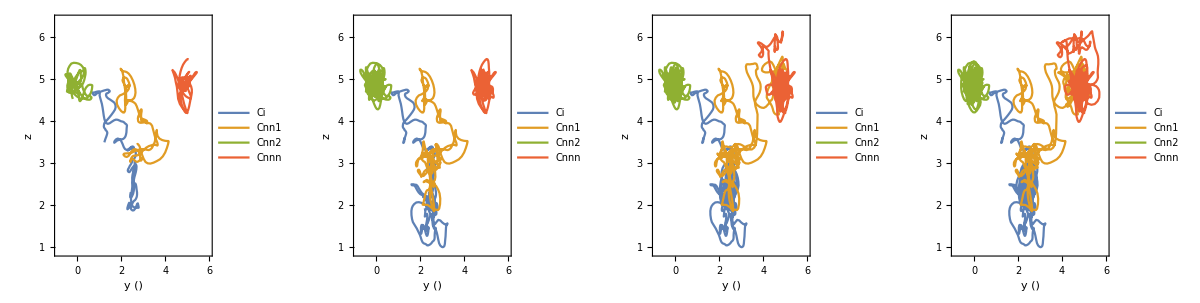

```mathematica
grid2d
```

```mathematica
(*Same-atom x-y correlation*)
Table[Table[Correlation[Transpose[selectedData[[j]][[i]]][[1]],Transpose[selectedData[[j]][[i]]][[2]]],{i,1,4}],{j,1,5}]//MatrixForm
```

(0.83528 | 0.525729 | 0.982159 | -0.849208
-0.837871 | -0.582207 | -0.217536 | 0.0185505
-0.703864 | -0.0793893 | -0.143813 | -0.0357953
-0.660065 | 0.569033 | -0.113336 | -0.458684
-0.614395 | 0.676447 | -0.129507 | -0.257402)

```mathematica
(*Atom1-atomi x-x correlation*)
Table[Table[Correlation[Transpose[selectedData[[j]][[1]]][[1]],Transpose[selectedData[[j]][[i]]][[1]]],{i,1,4}],{j,1,5}]//MatrixForm
```

(1. | -0.898116 | 0.460469 | -0.283364
1. | 0.680563 | 0.0226343 | -0.247583
1. | 0.368063 | -0.00932649 | -0.140155
1. | 0.262313 | -0.0117412 | -0.146266
1. | 0.297294 | -0.0469508 | -0.0385856)

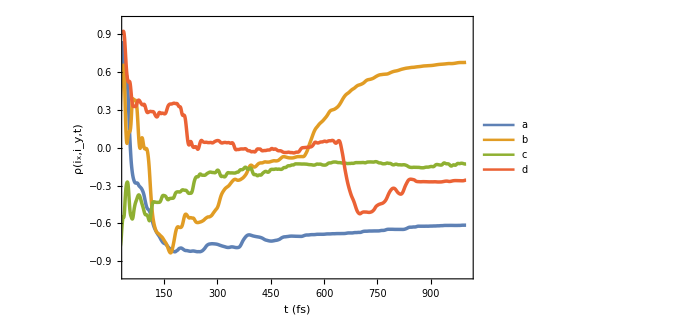

```mathematica
(*Same-atom x-y correlation function for each atom time evolution*)
plotOpts4={FrameLabel->{"t (fs)","ρ(i_x,i_y,t)"},Frame->True,AspectRatio->0.66,ImageSize->500,PlotLegends->Placed[{"a","b","c","d"},{0.5,0.75}],FrameStyle->Directive[Black,18,Thickness[0.003]],PlotStyle->{Thickness[0.005]},PlotRange->{{50,1000},Automatic}};
singleAtomCorrelation=ListLinePlot[Table[Table[Correlation[Transpose[selectedData[[5]][[j]]][[1]][[1;;i]],Transpose[selectedData[[5]][[j]]][[2]][[1;;i]]],{i,2,1000}],{j,1,4}],plotOpts4]
```

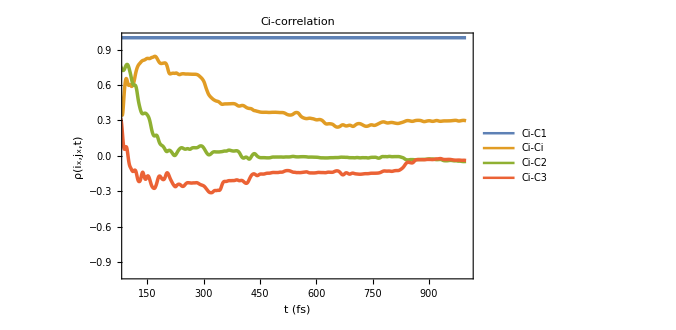

```mathematica
(*Atom1-atomi x-x correlation*)
plotOpts5={FrameLabel->{"t (fs)","ρ(i_x,j_x,t)"},Frame->True,AspectRatio->0.66,ImageSize->500,PlotLegends->Placed[{"Ci-C1","Ci-Ci","Ci-C2","Ci-C3"},{0.75,0.2}],FrameStyle->Directive[Black,18,Thickness[0.003]],PlotStyle->{Thickness[0.005]},PlotRange->{{100,1000},Automatic}};
singleAtomCorrelation=ListLinePlot[Table[Table[Correlation[Transpose[selectedData[[5]][[1]]][[1]][[1;;i]],Transpose[selectedData[[5]][[j]]][[1]][[1;;i]]],{i,2,1000}],{j,1,4}],plotOpts5,PlotLabel->"Ci-correlation"]
```

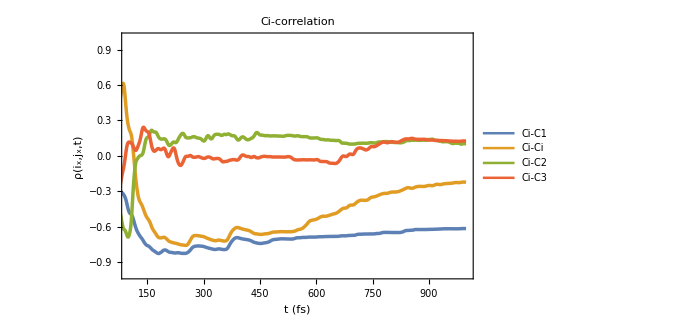

```mathematica
(*Atom1-atomi x-y correlation*)
plotOpts5={FrameLabel->{"t (fs)","ρ(i_x,j_x,t)"},Frame->True,AspectRatio->0.66,ImageSize->500,PlotLegends->Placed[{"Ci-C1","Ci-Ci","Ci-C2","Ci-C3"},{0.75,0.2}],FrameStyle->Directive[Black,18,Thickness[0.003]],PlotStyle->{Thickness[0.005]},PlotRange->{{100,1000},Automatic}};
singleAtomCorrelation=ListLinePlot[Table[Table[Correlation[Transpose[selectedData[[5]][[1]]][[1]][[1;;i]],Transpose[selectedData[[5]][[j]]][[2]][[1;;i]]],{i,2,1000}],{j,1,4}],plotOpts5,PlotLabel->"Ci-correlation"]
```

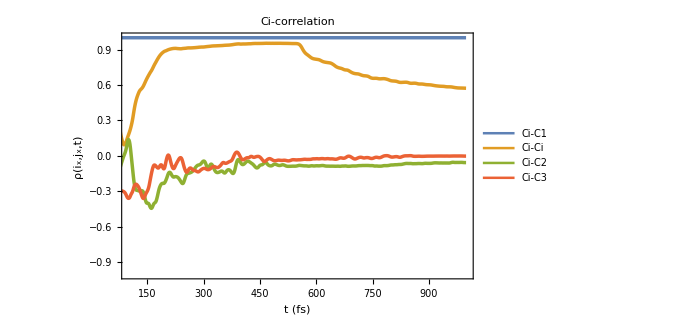

```mathematica
(*Atom1-atomi y-y correlation*)
plotOpts5={FrameLabel->{"t (fs)","ρ(i_x,j_x,t)"},Frame->True,AspectRatio->0.66,ImageSize->500,PlotLegends->Placed[{"Ci-C1","Ci-Ci","Ci-C2","Ci-C3"},{0.75,0.2}],FrameStyle->Directive[Black,18,Thickness[0.003]],PlotStyle->{Thickness[0.005]},PlotRange->{{100,1000},Automatic}};
singleAtomCorrelation=ListLinePlot[Table[Table[Correlation[Transpose[selectedData[[5]][[1]]][[2]][[1;;i]],Transpose[selectedData[[5]][[j]]][[2]][[1;;i]]],{i,2,1000}],{j,1,4}],plotOpts5,PlotLabel->"Ci-correlation"]
```

```mathematica
grid2d
```

-Graphics-

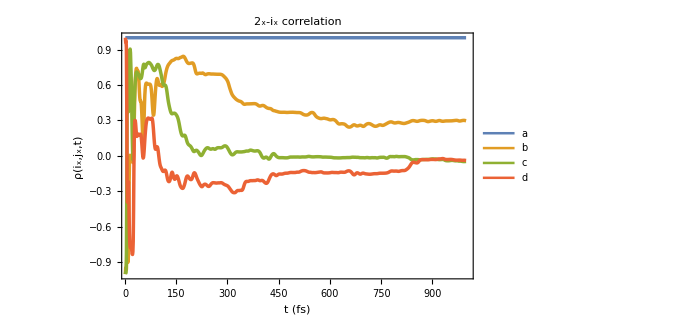

```mathematica
plotOpts5={FrameLabel->{"t (fs)","ρ(i_x,j_x,t)"},Frame->True,AspectRatio->0.66,ImageSize->500,PlotLegends->Placed[{"a","b","c","d"},{0.5,0.75}],FrameStyle->Directive[Black,18,Thickness[0.003]],PlotStyle->{Thickness[0.005]},PlotRange->{{10,1000},Automatic}};
singleAtomCorrelation=ListLinePlot[Table[Table[Correlation[Transpose[selectedData[[5]][[1]]][[1]][[1;;i]],Transpose[selectedData[[5]][[j]]][[1]][[1;;i]]],{i,2,1000}],{j,1,4}],plotOpts5,PlotLabel->"2_x-i_x correlation"]
```

```mathematica
(*Rahman-parinello - (<u1u2≥kT/K12)
```

```mathematica
xx=Table[(Transpose[selectedData[[5]][[1]]][[1]][[i]]-Transpose[selectedData[[5]][[1]]][[1]][[1]])*(Transpose[selectedData[[5]][[2]]][[1]][[i]]-Transpose[selectedData[[5]][[2]]][[1]][[1]]),{i,1,1000}];
```

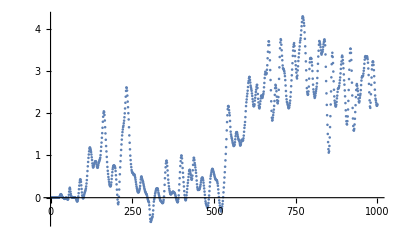

```mathematica
ListPlot@xx
```